# Analytic saddle point results for the BEC-BCS crossover in 3D

In this notebook the analytical solutions for the saddle-point treatment of the BEC-BCS crossover is given. The relevant quantities (gap, chemical potential, interaction strength, correlation length) are all determined as a function of the crossover parameter x_0=μ/Δ and hence can also be related to each other.
The results implemented here are based on 
M. Marini, F. Pistolesi, G.-C. Strinati, European Physical Journal B 1, 151-159 (1998).

The results are expressed in dimensionless units, obtained by setting ℏ = 2m = k_F = 1. Here m is the mass of an individual fermion, and the Fermi wavenumber is fixed by the total density, through k_F = (3 π^2 n)^(1/3). This means that energies (the gap, the chemical potential) are expressed in units E_F=(ℏ k_F)^2/(2m) .

## Auxiliary functions

Start by initializing these functions, eqs. (25),(27) of the paper mentioned above, in which we use (26) and (19).

```mathematica
i6[x0_]:=1./(2(1+x0^2)^(1/4))EllipticF[Pi/2, 1/2(1+x0/(√(1+x0^2)))];
i5[x0_]:=With[ {κ=1/2(1+x0/(√(1+x0^2)))}, (1.+x0^2)^(1/4)EllipticE[Pi/2,κ]-1./(2(√(1+x0^2)+x0)(1+x0^2)^(1/4))EllipticF[Pi/2,κ]];
```

Note that Mathematica implements the elleptic integrals differently: the second argument is κ^2 in the notation of Marini et al, as can be seen from comparing the Taylor expansions reported in that paper and in Mathematica’s help page for EllipticE and EllipticF.

## Results as a function of x_0=μ/Δ

The gap is given by :

```mathematica
Δ[x0_]:=(x0 i5[x0]+i6[x0])^(-2/3);
```

Next, we have the chemical potential :

```mathematica
μ[x0_]:=x0(x0 i5[x0]+i6[x0])^(-2/3);
```

Then, the interaction parameter  1/(k_F a_s):

```mathematica
kfas[x0_]:=-4/π(x0 i6[x0]-i5[x0])/(x0 i5[x0]+i6[x0])^(1/3);
```

The pair correlation length k_F ξ_pair  is :

```mathematica
ξpair[x0_]:=√(1/2(1+((√(1+x0^2)+x0)/2)^2))(x0 i5[x0]+i6[x0])^(1/3)/((1+x0^2)^(1/4));
```

The phase coherence length k_F ξ_phase  is :

```mathematica
ξphase[x0_]:=With[ {ii5=i5[x0],ii6=i6[x0]},√((x0 ii5+ii6)^(2/3)/(12 ii5)(2 ii6+(1+4 x0^2)/(3(1+x0^2))(ii6+x0 ii5)))];
```

Finally, the sound velocity (long wavelengh), in units of the fermi velocity v_F= ℏ k_F/m is :

```mathematica
c[x0_]:=With[ {ii5=i5[x0],ii6=i6[x0]},√(1/3((x0 ii5+ii6)^(1/3) ii5)/(ii5^2+ii6^2))];
```

note that this departs from our usual units (that set 2m=1 rather than m=1), where the fermi velocity has a value of v_F=2 .

## Visualization of the results

The key quantity is the crossover parameter x_0 . Usually, experimenters plot their measurements as a function of 1/(k_F a_s),  so this dependency is crucial.

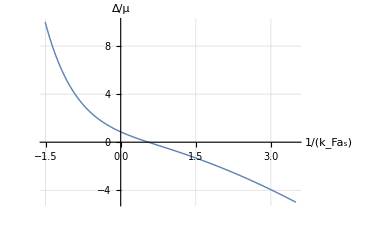

```mathematica
ListPlot[ Table[ {kfas[x0],x0}, {x0,-5,10,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"1/(k_Fa_s)","μ/Δ"}, BaseStyle->FontSize->14, PlotStyle->Thick,GridLines->Automatic ]
```

Using Table and Listplot we can not plot different quantities against each other, for example the gap versus the interaction parameter

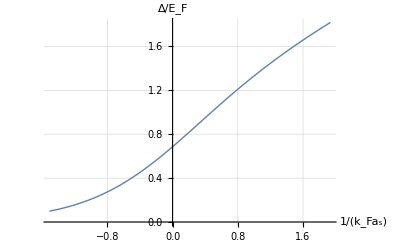

```mathematica
ListPlot[ Table[ {kfas[x0],Δ[x0]}, {x0,-2,10,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"1/(k_Fa_s)","Δ/E_F"}, BaseStyle->FontSize->14, PlotStyle->Thick,GridLines->Automatic ]
```

or the chemical potential versus interaction parameter

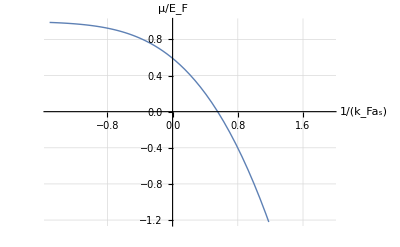

```mathematica
ListPlot[ Table[ {kfas[x0],μ[x0]}, {x0,-2,10,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"1/(k_Fa_s)","μ/E_F"}, BaseStyle->FontSize->14, PlotStyle->Thick,GridLines->Automatic ]
```

The phase and pair correlation functions

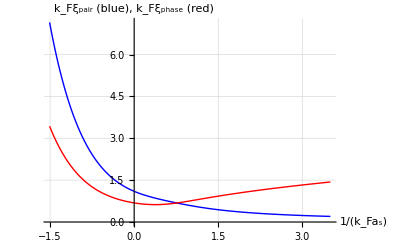

```mathematica
ListPlot[ {Table[ {kfas[x0],ξpair[x0]}, {x0,-5,10,0.1} ],Table[ {kfas[x0],ξphase[x0]}, {x0,-5,10,0.1} ]}, Joined->True, AxesStyle->Black, AxesLabel->{"1/(k_Fa_s)","k_Fξ_pair (blue), k_Fξ_phase (red)"}, BaseStyle->FontSize->14, PlotStyle->{{Thick,Blue},{Thick,Red}}, GridLines->Automatic ]
```

Or, versus each other:

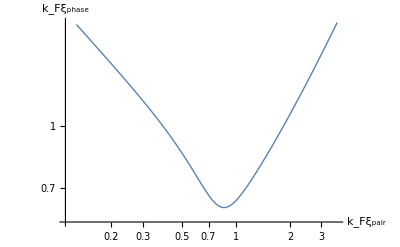

```mathematica
ListLogLogPlot[ Table[ {ξpair[x0],ξphase[x0]}, {x0,-10,5,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"k_Fξ_pair","k_Fξ_phase"}, BaseStyle->FontSize->14, PlotStyle->Thick, GridLines->Automatic ]
```

Finally, the sound velocity

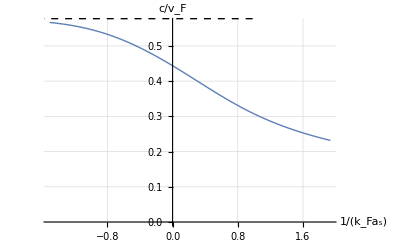

```mathematica
ListPlot[ Table[ {kfas[x0],c[x0]}, {x0,-2,10,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"1/(k_Fa_s)","c/v_F"}, BaseStyle->FontSize->14, PlotStyle->Thick, GridLines->Automatic, Epilog->{Dashed,Line[{{-2,1/√3},{1,1/√3}}]} ]
```

## All-in-one module, as function of x_0=μ/Δ

For faster computation or if you do not want to copy-paste individual lines, the following module can be useful. It puts together all that we computed before. It’s input is simply the interaction strength x_0= Δ/μ  and it ouputs a list, 
   { Δ/E_F , μ/E_F , 1/(k_F a_s) , k_Fξ_pair , k_Fξ_phase , c/v_F }

Copy-paste the blue block below to incorporate it in your own work note.

```mathematica
saddlepoint0[ x0_ ]:=Module[ (*input Subscript[x, 0] = Δ/μ and returns {Δ/Subscript[E, F] , μ/Subscript[E, F] , 1/(Subscript[k, F] Subscript[a, s]), Subscript[k, F] Subscript[ξ, pair] , Subscript[k, F] Subscript[ξ, phase] , c/Subscript[v, F]}*)
{ii6=1./(2(1+x0^2)^(1/4))EllipticF[Pi/2, 1/2(1+x0/(√(1+x0^2)))],
ii5=With[ {κ=1/2(1+x0/(√(1+x0^2)))}, (1.+x0^2)^(1/4)EllipticE[Pi/2,κ]-1./(2(√(1+x0^2)+x0)(1+x0^2)^(1/4))EllipticF[Pi/2,κ]]},
{(x0 ii5+ii6)^(-2/3), 
x0(x0 ii5+ii6)^(-2/3),
-4/π(x0 ii6-ii5)/(x0 ii5+ii6)^(1/3),
√(1/2(1+((√(1+x0^2)+x0)/2)^2))(x0 ii5+ii6)^(1/3)/((1+x0^2)^(1/4)),
√((x0 ii5+ii6)^(2/3)/(12 ii5)(2 ii6+(1+4 x0^2)/(3(1+x0^2))(ii6+x0 ii5))),
√(1/3((x0 ii5+ii6)^(1/3) ii5)/(ii5^2+ii6^2))}]
```

```mathematica
saddlepoint0[ 0.11 ]
```

{0.999175,0.109909,0.473457,0.80765,0.626708,0.375404}

## Results as function of the interaction parameter

As shown in the graphs above, very often results are plotted as a function of the interaction parameter. For that, we need to invert the formula that links the interaction parameter with the crossover parameter. This cannot be done analytically, as it is a transcendent equation. But since it is monotonic, it is not too hard to use general root finding algorithms

```mathematica
Δoverμ[ g_ ]:=(x /. FindRoot[ kfas[x]==g, {x,-1,5}])
```

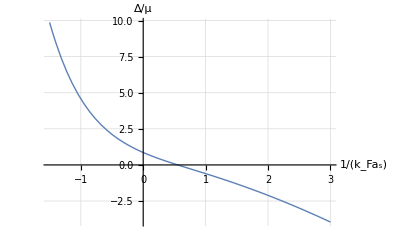

```mathematica
Plot[ Δoverμ[ g ], {g,-1.5,3}, AxesStyle->Black, AxesLabel->{"1/(k_Fa_s)","Δ/μ"}, BaseStyle->FontSize->14, PlotStyle->Thick,GridLines->Automatic ]
```

Now, we can again compute, in a more circuitous way, all the quantities,

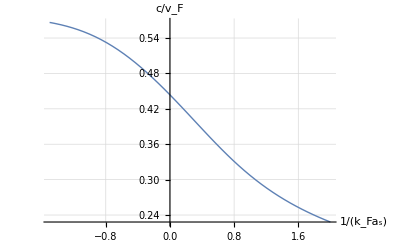

```mathematica
Plot[ c[Δoverμ[g]], {g,-1.5,2} , AxesStyle->Black, AxesLabel->{"1/(k_Fa_s)","c/v_F"}, BaseStyle->FontSize->14, PlotStyle->Thick, GridLines->Automatic, Epilog->{Dashed,Line[{{-2,1/√3},{1,1/√3}}]} ]
```

## Similar module, as function of 1/(k_F a_s)

If you want to find the results as a function of the interaction strength, you need a few more auxiliary functions. In that case, you can copy the green cells below.

```mathematica
i6[x0_]:=1./(2(1+x0^2)^(1/4))EllipticF[Pi/2, 1/2(1+x0/(√(1+x0^2)))];
i5[x0_]:=With[ {κ=1/2(1+x0/(√(1+x0^2)))}, (1.+x0^2)^(1/4)EllipticE[Pi/2,κ]-1./(2(√(1+x0^2)+x0)(1+x0^2)^(1/4))EllipticF[Pi/2,κ]];
Δoverμ[ g_ ]:=(x /. FindRoot[ -4/π(x i6[x]-i5[x])/(x i5[x]+i6[x])^(1/3)==g, {x,-1,5}])
```

```mathematica
saddlepoint[ kfasinv_ ]:=Module[ (*input 1/(Subscript[k, F] Subscript[a, s]) and returns {Δ/Subscript[E, F] , μ/Subscript[E, F] , Subscript[k, F] Subscript[ξ, pair] , Subscript[k, F] Subscript[ξ, phase] , c/Subscript[v, F]}*)
{ii5,ii6,x0},
x0=Δoverμ[kfasinv]; 
ii6=1./(2(1+x0^2)^(1/4))EllipticF[Pi/2, 1/2(1+x0/(√(1+x0^2)))];
ii5=With[ {κ=1/2(1+x0/(√(1+x0^2)))}, (1.+x0^2)^(1/4)EllipticE[Pi/2,κ]-1./(2(√(1+x0^2)+x0)(1+x0^2)^(1/4))EllipticF[Pi/2,κ]];
{(x0 ii5+ii6)^(-2/3), 
x0(x0 ii5+ii6)^(-2/3),
√(1/2(1+((√(1+x0^2)+x0)/2)^2))(x0 ii5+ii6)^(1/3)/((1+x0^2)^(1/4)),
√((x0 ii5+ii6)^(2/3)/(12 ii5)(2 ii6+(1+4 x0^2)/(3(1+x0^2))(ii6+x0 ii5))),
√(1/3((x0 ii5+ii6)^(1/3) ii5)/(ii5^2+ii6^2))}]
```

# Analytic saddle point results for the BEC-BCS crossover in 2D

In this second part of the notebook the analytical solutions for the saddle-point treatment of the BEC-BCS crossover in 2D is given. The relevant quantities (gap, chemical potential, interaction strength, correlation length) are all determined as a function of the crossover parameter x_0=μ/Δ and hence can also be related to each other. The derivation predates the paper of Marini et al., but was also summarized in their notations in the appendix of 
M. Marini, F. Pistolesi, G.-C. Strinati, European Physical Journal B 1, 151-159 (1998).

The results are again expressed in dimensionless units, obtained by setting ℏ = 2m = k_F = 1. Here m is the mass of an individual fermion, and the Fermi wavenumber is fixed by the total density, through k_F = √(2π n). This means that energies (the gap, the chemical potential) are expressed in units E_F=(ℏ k_F)^2/(2m) .

The control parameter for the interaction strength is no longer the scattering length, but the binding energy E_b of the molecule, present at any scattering length in 2D. Here it is expressed as E_b/E_F . Traditionally, E_b/E_F<2 is considered to be on the BCS side, whereas E_b/E_F>2 is the BEC side.

## 2D results as a function of x_0=μ/Δ

The gap is given by :

```mathematica
Δ2D[x0_]:=2/(√(1+x0^2)+x0);
```

Next, we have the chemical potential :

```mathematica
μ2D[x0_]:=x0 2/(√(1+x0^2)+x0);
```

Then, the bound state energy E_b/E_F :

```mathematica
ebEf[x0_]:=2(√(1+x0^2)-x0)/(√(1+x0^2)+x0);
```

The pair correlation length k_F ξ_pair  is :

```mathematica
ξpair2D[x0_]:=√((√(1+x0^2)+x0)/4(x0+(2+x0^2)/(1+x0^2)(Pi/2+ArcTan[x0])^-1));
```

The phase coherence length k_F ξ_phase  is :

```mathematica
ξphase2D[x0_]:=√((√(1+x0^2))/12(x0+(x0^4+3 x0^2+1)/((1+x0^2)^(3/2)))) ;
```

Finally, the sound velocity (long wavelengh), in units of the fermi velocity v_F= ℏ k_F/m is independent of the binding energy:

```mathematica
c2D[x0_]:=0.5;
```

## 2D results visualized

The key quantity is the crossover parameter x_0 . Usually, experimenters plot their measurements as a function of 1/(k_F a_s),  so this dependency is crucial.

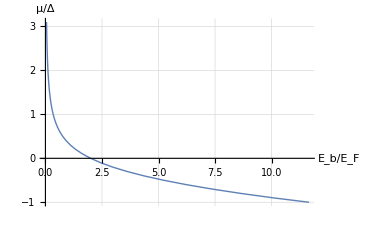

```mathematica
ListPlot[ Table[ {ebEf[x0],x0}, {x0,-1,3.1,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"E_b/E_F","μ/Δ"}, BaseStyle->FontSize->14, PlotStyle->Thick,GridLines->Automatic ]
```

Using Table and Listplot we can not plot different quantities against each other, for example the gap versus the interaction parameter

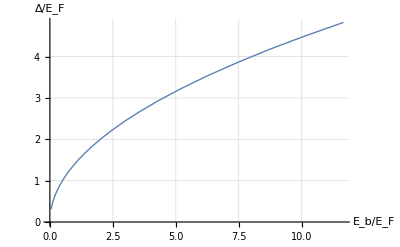

```mathematica
ListPlot[ Table[ {ebEf[x0],Δ2D[x0]}, {x0,-1,3.1,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"E_b/E_F","Δ/E_F"}, BaseStyle->FontSize->14, PlotStyle->Thick,GridLines->Automatic ]
```

or the chemical potential versus interaction parameter

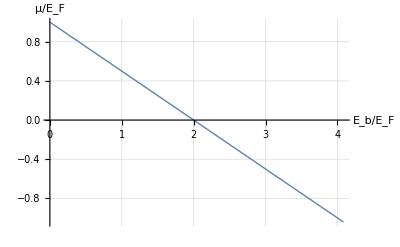

```mathematica
ListPlot[ Table[ {ebEf[x0],μ2D[x0]}, {x0,-2,10,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"E_b/E_F","μ/E_F"}, BaseStyle->FontSize->14, PlotStyle->Thick,GridLines->Automatic ]
```

The phase and pair correlation functions

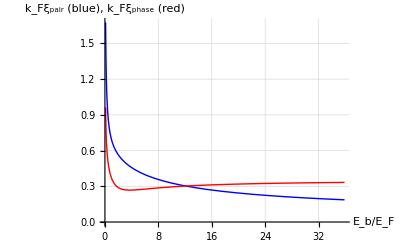

```mathematica
ListPlot[ {Table[ {ebEf[x0],ξpair2D[x0]}, {x0,-2,2.1,0.1} ],Table[ {ebEf[x0],ξphase2D[x0]}, {x0,-2,2.1,0.1} ]}, Joined->True, AxesStyle->Black, AxesLabel->{"E_b/E_F","k_Fξ_pair (blue), k_Fξ_phase (red)"}, BaseStyle->FontSize->14, PlotStyle->{{Thick,Blue},{Thick,Red}}, GridLines->Automatic ]
```

Or, versus each other:

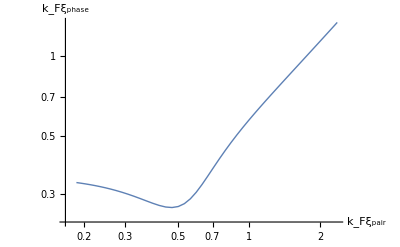

```mathematica
ListLogLogPlot[ Table[ {ξpair2D[x0],ξphase2D[x0]}, {x0,-2,3.1,0.1} ], Joined->True, AxesStyle->Black, AxesLabel->{"k_Fξ_pair","k_Fξ_phase"}, BaseStyle->FontSize->14, PlotStyle->Thick, GridLines->Automatic ]
```

```mathematica
Solve[ energ==2(√(1+x0^2)-x0)/(√(1+x0^2)+x0), x0 ]
```

{{x0→-(-2+energ)/(2 √2 √energ)},{x0→(-2+energ)/(2 √2 √energ)}}

## Module for all 2D quantities, as function of E_b/E_F

```mathematica
saddlepoint2D[ ebef_ ]:=Module[ (*input Subscript[E, b]/Subscript[E, F] and returns {Δ/Subscript[E, F] , μ/Subscript[E, F] , Subscript[k, F] Subscript[ξ, pair] , Subscript[k, F] Subscript[ξ, phase] *)
{x0=(ebef-2.)/(√(8. ebef))},
{2/(√(1+x0^2)+x0), 
x0 2/(√(1+x0^2)+x0),
√((√(1+x0^2)+x0)/4(x0+(2+x0^2)/(1+x0^2)(Pi/2+ArcTan[x0])^-1)),
√((√(1+x0^2))/12(x0+(x0^4+3 x0^2+1)/((1+x0^2)^(3/2))))}];
```